```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

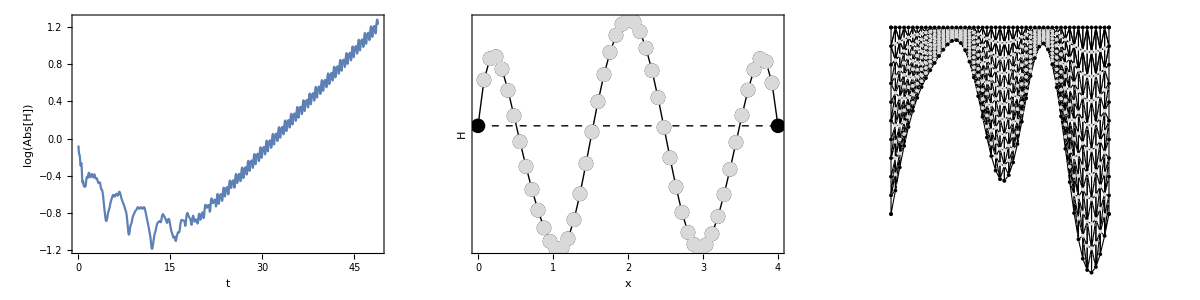

24.000000 1.000000 0.500000 3.989474 3.926991 1.750000 47.000000

```mathematica
filebase="data/rectanglerandom";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-1;
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]}}]
lst[[-1]]
```

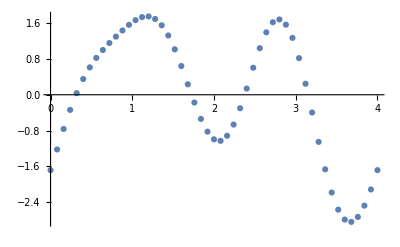

1.75

InterpolatingFunction[…]

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,1.52796,1.38673,0.97207,6.52093×10^-6}

{0.0000220135,-1.62996,-2.68035,0.940659,0.0000212789}

0.0000220135

```mathematica
ListPlot[mesh[[1,bottom]]]
Max[mesh[[1,bottom,2]]]
h=Interpolation[mesh[[1,bottom]]]
Table[NIntegrate[h[x]*Sin[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
Table[NIntegrate[h[x]*Cos[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
NIntegrate[h[x],{x,0,length}]
```

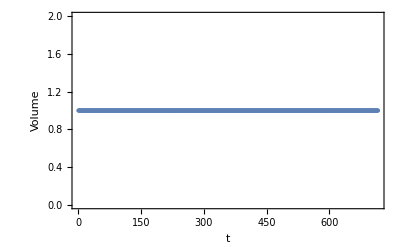

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[2*Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496,20.4204,21.9911,23.5619,25.1327,26.7035,28.2743,29.8451,31.4159}

{13.5484,23.1977,35.0902,49.33,65.6822,83.9231,103.874,125.396,148.377,172.725,198.365,225.233,253.271,282.433,312.675,343.958,376.249,409.516,443.731,478.868}

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{8.64676,13.5484,18.1475,23.1977,28.8395,35.0902,41.9305,49.33,57.2571,65.6822,74.5787,83.9231,93.6945,103.874,114.447,125.396,136.71,148.377,160.385,172.725}

Generate box substrate

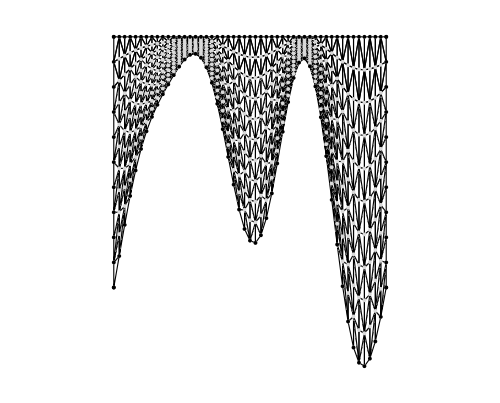

```mathematica
filebase="data/rectanglerandom";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-1;
mesh2=mesh[[m]];
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]
```

```mathematica
modes=ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate modes"][[1]]+1]]]];
subss=ConstantArray[0.,{8,8}]
subsc=Normal[SparseArray[Table[{i,1}->modes[[i]],{i,1,8}],{8,8}]]
subcs=ConstantArray[0.,{8,8}]
subcc=Normal[SparseArray[Table[{i,1}->modes[[8+i]],{i,1,8}],{8,8}]]
Export["boxsubstrate.dat",Join[subss,subsc,subcs,subcc]]
```

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{{-1.35279,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.800571,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.726618,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.509466,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-0.854026,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{-1.40446,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0.492995,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

boxsubstrate.dat

Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Periodic sweep plots

sr1

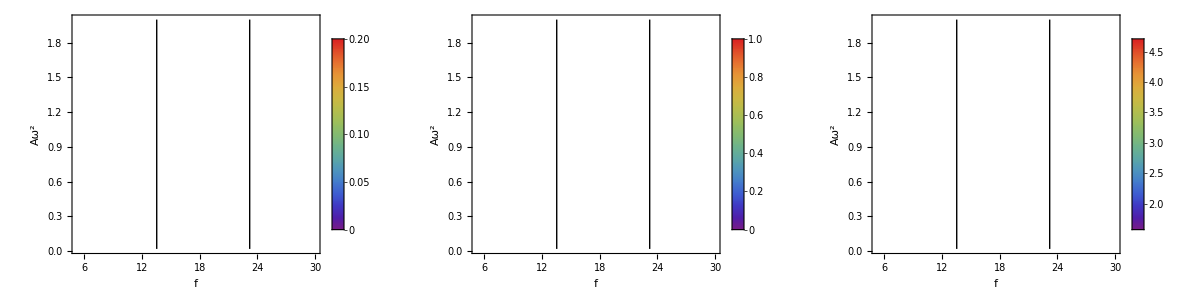

```mathematica
filebase="sr1"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

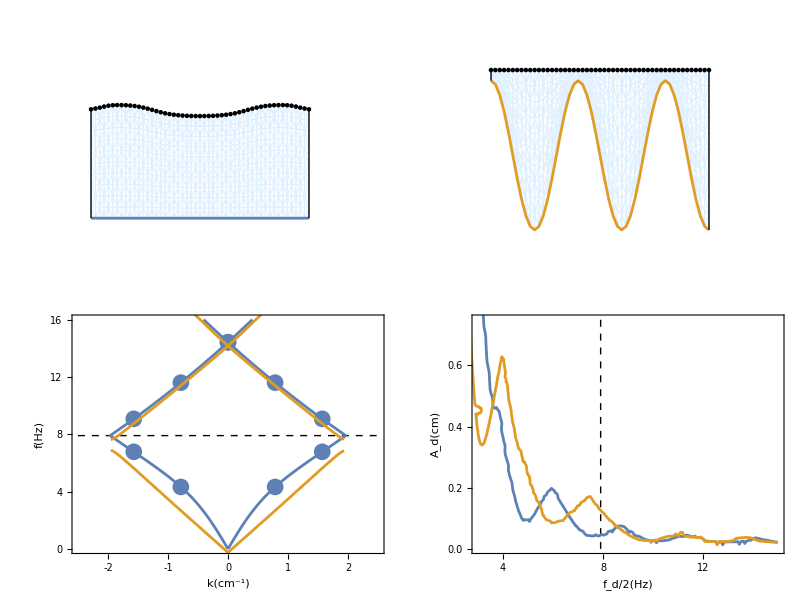

rectanglegap.pdf

```mathematica
gap=2*Pi/length*5/4;
inhomogeneous=ToExpression[Import["inviscidgap.dat","CSV"]];
p1=Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]],ListPlot[inhomogeneous,Joined->True,Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]],Prolog->{Black,Dashed,Line[{{-2.5,(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi)},{2.5,(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi)}}]}];
filebases={"sr3","sr4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}},Prolog->{Black,Dashed,Line[{{(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi),0},{(g*gap*Tanh[gap*height]*(1+σ/g*gap^2))^(1/2)/(2*Pi),2}}]}],{i,1,Length[sweeps]}];
filebase="data/rectangleinhomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,1.75},{0,2.0}}],Line[{{length,-1.75},{length,2.0}}]}];
filebase="data/rectanglehomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-50;
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,2.0}}],Line[{{length,0},{length,2.0}}]}];
filebase="sa1";
fsweeps=Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}];
p5=ListPlot[Table[{1.75*i/100,MinimalBy[Cases[fsweeps[[All,i]],u_/;u[[4]]>0],#[[2]]&][[1,2]]*980/(2*Pi*16)^2},{i,1,100}],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],AspectRatio->1,LabelStyle->Directive[14,Black],FrameLabel->{Subscript[A,s],Subsuperscript[A,d,c]},ImageSize->150,PlotStyle->Directive[Black],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.1,0.05}],Table[{i,""},{i,0,0.1,0.05}]},{Table[{i,PaddedForm[i,{2,2}]},{i,0,1.75,0.75}],Table[{i,""},{i,0,1.75,0.75}]}}];
p=Grid[{{p4,p2},{p1,Show[p3,Epilog->Inset[p5,{10,0.4},{0,0}]]}}]
Export["rectanglegap.pdf",p]
```

```mathematica
Count[sweeps[[1,All,{1,2,4}]],u_/;u[[3]]>0]
Count[sweeps[[2,All,{1,2,4}]],u_/;u[[3]]>0]
```

6248

5728

```mathematica
Total[980/(2*Pi*#[[1]])^2*2.0/100*(30-5)/100&/@Cases[sweeps[[1,All,{1,2,4}]],u_/;u[[3]]>0]]
Total[980/(2*Pi*#[[1]])^2*2.0/100*(30-5)/100&/@Cases[sweeps[[2,All,{1,2,4}]],u_/;u[[3]]>0]]
```

4.19691

4.52069

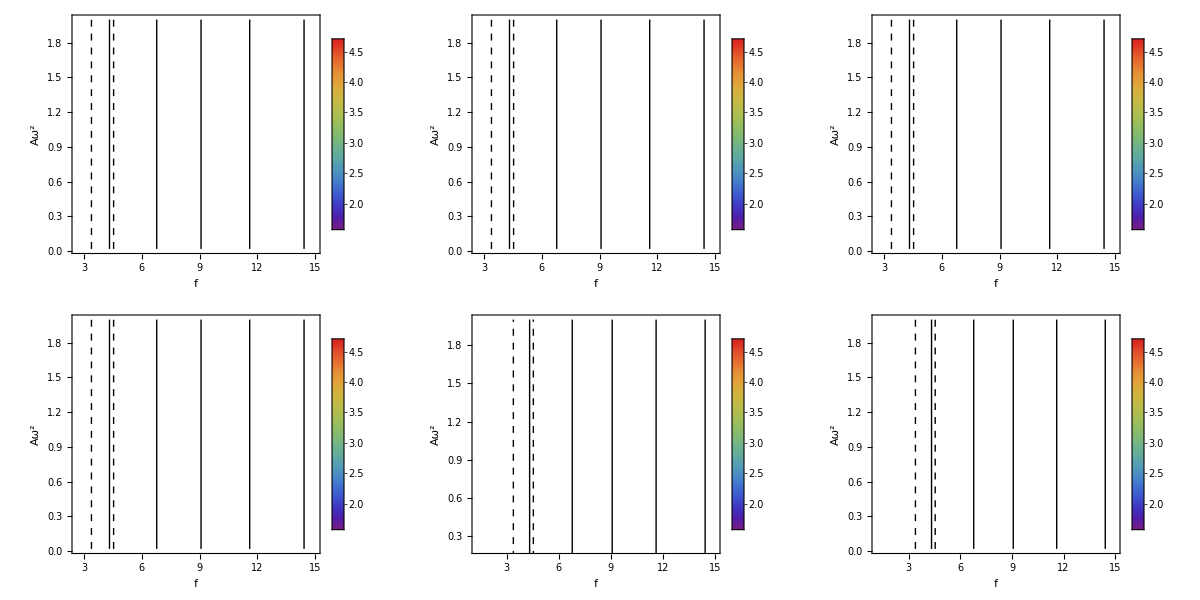

pitfall.pdf

```mathematica
filebases={"sr1","sr2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
filebases={"sr7","nr3"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
filebases={"sr3","r2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p3=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
p=Grid[Transpose[{p1,p2,p3}]]
Export["pitfall.pdf",p]
```

Random substrates

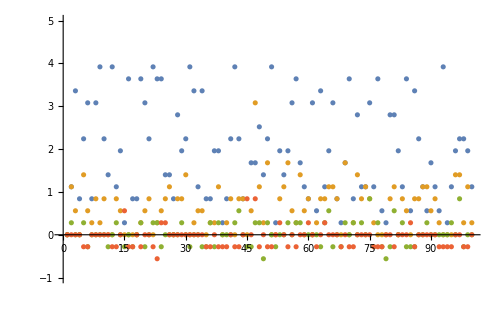

{47.,75.,97.,81.,9.,72.,24.,63.,57.,50.,42.,22.,3.,84.,8.,66.,19.,86.,5.,56.,55.,48.,93.,65.,51.,34.,32.,31.,12.,30.,28.,23.,77.,69.,70.,43.,16.,80.,20.,96.,58.,41.,29.,21.,6.,61.,53.,38.,10.,87.,99.,64.,54.,25.,14.,2.,26.,88.,83.,74.,73.,90.,46.,89.,82.,91.,60.,13.,37.,98.,44.,67.,59.,33.,100.,49.,71.,11.,7.,95.,36.,27.,4.,40.,18.,76.,92.,85.,62.,15.,35.,17.,78.,1.,52.,94.,39.,79.,68.,45.}

Part::partd: Part specification random⟦1⟧ is longer than depth of object.

Part::partd: Part specification random⟦4⟧ is longer than depth of object.

Part::partd: Part specification random⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification random⟦1⟧ is longer than depth of object.

Part::partd: Part specification random⟦4⟧ is longer than depth of object.

Part::partd: Part specification random⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification random⟦1⟧ is longer than depth of object.

Part::partd: Part specification random⟦4⟧ is longer than depth of object.

Part::partd: Part specification random⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification random⟦1⟧ is longer than depth of object.

Part::partd: Part specification random⟦4⟧ is longer than depth of object.

Part::partd: Part specification random⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Clear[mins]
Clear[maxes]
filebases={"sr3","sr4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
filebase="r1";
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6]&/@random)[[All,All,5]]]];
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
Manipulate[ListPlot[{Cases[random[[1]],u_/;u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{0,30},{0,5}}],{m,1,Length[random],1}]
Reverse[SortBy[seeds,Total[shifts[[1;;4,First@FirstPosition[seeds,#]]]]&]]
```

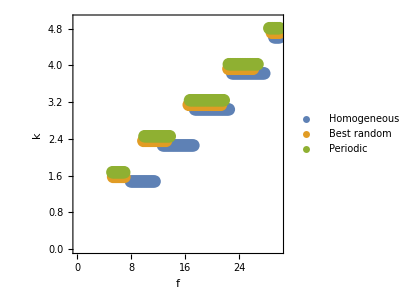

```mathematica
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==1.0&&u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[47]],u_/;u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==1.0&&u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{0,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyles->Directive[16,Black,FontFamily["Arial"]],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```

```mathematica
Reverse[SortBy[Range[Length[seeds]],shifts[[2,#]]&]]
Reverse[SortBy[seeds,shifts[[2,First@FirstPosition[seeds,#]]]&]]
```

{47,50,69,55,97,30,5,72,58,96,99,89,88,81,74,66,65,48,38,54,26,2,86,80,75,64,63,44,41,21,8,91,87,83,73,67,60,53,43,29,25,13,10,28,84,56,46,34,24,20,14,6,3,90,59,33,57,49,37,9,100,98,92,76,71,62,40,36,32,23,19,7,93,82,79,78,77,70,68,52,51,45,42,35,31,27,22,16,15,12,11,4,1,95,94,85,61,39,18,17}

{47.,50.,69.,55.,97.,30.,5.,72.,58.,96.,99.,89.,88.,81.,74.,66.,65.,48.,38.,54.,26.,2.,86.,80.,75.,64.,63.,44.,41.,21.,8.,91.,87.,83.,73.,67.,60.,53.,43.,29.,25.,13.,10.,28.,84.,56.,46.,34.,24.,20.,14.,6.,3.,90.,59.,33.,57.,49.,37.,9.,100.,98.,92.,76.,71.,62.,40.,36.,32.,23.,19.,7.,93.,82.,79.,78.,77.,70.,68.,52.,51.,45.,42.,35.,31.,27.,22.,16.,15.,12.,11.,4.,1.,95.,94.,85.,61.,39.,18.,17.}

```mathematica
(*Find the gaps between tongues here, and plot as a function of samp *)
filebase="sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
Manipulate[ListPlot[Cases[Flatten[fsweeps,1],u_/;u[[6]]==substrates[[m]]&&u[[4]]>0.5&&u[[3]]<0.6][[All,{1,5}]],PlotRange->{{0,30},{0,5}}],{m,1,Length[substrates],1}]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[fsweeps,1].

Part::partd: Part specification fsweeps⟦6⟧ is longer than depth of object.

Part::partd: Part specification substrates⟦1⟧ is longer than depth of object.

Part::partd: Part specification fsweeps⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[fsweeps,1].

Part::partd: Part specification fsweeps⟦6⟧ is longer than depth of object.

Part::partd: Part specification substrates⟦1⟧ is longer than depth of object.

Part::partd: Part specification fsweeps⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
wavenumbers
```

{1.5708,2.35619,3.14159,3.92699,4.71239}

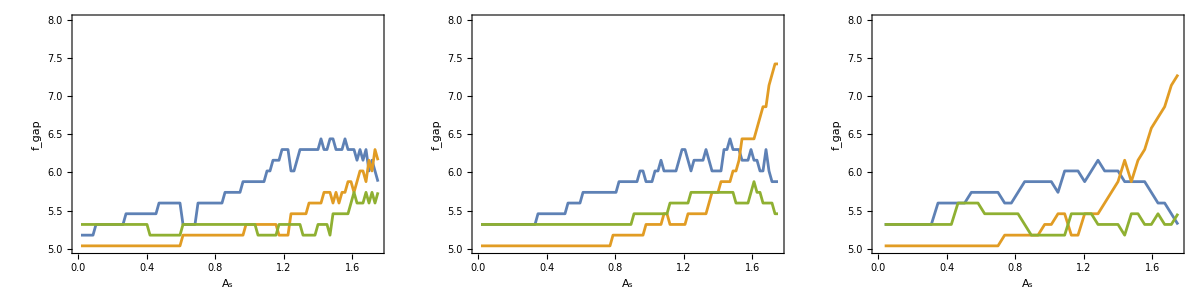

```mathematica
filebase="sa2";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p1=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p2=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sa4";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p3=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];
Grid[{{p1,p2,p3}}]
```

```mathematica
(Length/@fsweeps)
```

{45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45}

```mathematica
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
```

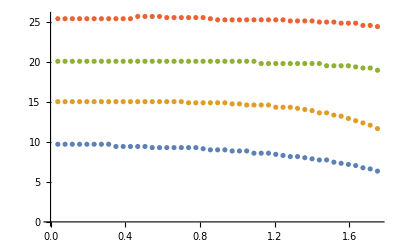

```mathematica
ListPlot[means]
```

```mathematica
mins
```

{{{0.0175,8.44},{0.035,8.44},{0.0525,8.44},{0.07,8.44},{0.0875,8.44},{0.105,8.44},{0.1225,8.44},{0.14,8.44},{0.1575,8.44},{0.175,8.44},{0.1925,8.44},{0.21,8.44},{0.2275,8.44},{0.245,8.44},{0.2625,8.44},{0.28,8.44},{0.2975,8.44},{0.315,8.44},{0.3325,8.44},{0.35,8.44},{0.3675,8.44},{0.385,8.44},{0.4025,8.44},{0.42,8.44},{0.4375,8.44},{0.455,8.44},{0.4725,8.44},{0.49,8.44},{0.5075,8.44},{0.525,8.16},{0.5425,8.16},{0.56,8.16},{0.5775,8.16},{0.595,8.16},{0.6125,8.16},{0.63,8.16},{0.6475,8.16},{0.665,8.16},{0.6825,8.16},{0.7,8.16},{0.7175,8.16},{0.735,8.16},{0.7525,8.16},{0.77,8.16},{0.7875,8.16},{0.805,8.16},{0.8225,7.88},{0.84,7.88},{0.8575,7.88},{0.875,7.88},{0.8925,7.88},{0.91,7.88},{0.9275,7.88},{0.945,7.88},{0.9625,7.88},{0.98,7.88},{0.9975,7.88},{1.015,7.88},{1.0325,7.6},{1.05,7.6},{1.0675,7.6},{1.085,7.6},{1.1025,7.6},{1.12,7.6},{1.1375,7.6},{1.155,7.6},{1.1725,7.6},{1.19,7.32},{1.2075,7.32},{1.225,7.32},{1.2425,7.32},{1.26,7.32},{1.2775,7.32},{1.295,7.32},{1.3125,7.32},{1.33,7.32},{1.3475,7.32},{1.365,7.32},{1.3825,7.32},{1.4,7.32},{1.4175,7.32},{1.435,6.76},{1.4525,6.76},{1.47,6.76},{1.4875,6.76},{1.505,6.76},{1.5225,6.48},{1.54,6.48},{1.5575,6.48},{1.575,6.48},{1.5925,6.2},{1.61,6.2},{1.6275,6.2},{1.645,6.2},{1.6625,5.92},{1.68,5.92},{1.6975,5.92},{1.715,5.92},{1.7325,5.64},{1.75,5.64}},{{0.0175,13.2},{0.035,13.2},{0.0525,13.2},{0.07,13.2},{0.0875,13.2},{0.105,13.2},{0.1225,13.2},{0.14,13.2},{0.1575,13.2},{0.175,13.2},{0.1925,13.2},{0.21,13.2},{0.2275,13.2},{0.245,13.2},{0.2625,13.2},{0.28,13.2},{0.2975,13.2},{0.315,13.2},{0.3325,13.2},{0.35,13.2},{0.3675,13.2},{0.385,13.2},{0.4025,13.2},{0.42,13.2},{0.4375,13.2},{0.455,13.2},{0.4725,13.2},{0.49,13.2},{0.5075,13.2},{0.525,13.2},{0.5425,13.2},{0.56,13.2},{0.5775,13.2},{0.595,13.2},{0.6125,13.2},{0.63,13.2},{0.6475,13.2},{0.665,13.2},{0.6825,13.2},{0.7,13.2},{0.7175,13.2},{0.735,13.2},{0.7525,13.2},{0.77,13.2},{0.7875,13.2},{0.805,13.2},{0.8225,13.2},{0.84,13.2},{0.8575,13.2},{0.875,13.2},{0.8925,13.2},{0.91,13.2},{0.9275,13.2},{0.945,13.2},{0.9625,13.2},{0.98,12.92},{0.9975,12.92},{1.015,12.92},{1.0325,12.92},{1.05,12.92},{1.0675,12.92},{1.085,12.92},{1.1025,12.92},{1.12,12.92},{1.1375,12.92},{1.155,12.92},{1.1725,12.92},{1.19,12.92},{1.2075,12.92},{1.225,12.64},{1.2425,12.64},{1.26,12.64},{1.2775,12.64},{1.295,12.64},{1.3125,12.64},{1.33,12.64},{1.3475,12.64},{1.365,12.36},{1.3825,12.36},{1.4,12.36},{1.4175,12.36},{1.435,12.36},{1.4525,12.36},{1.47,12.36},{1.4875,12.36},{1.505,12.36},{1.5225,12.08},{1.54,11.8},{1.5575,11.8},{1.575,11.8},{1.5925,11.8},{1.61,11.52},{1.6275,11.52},{1.645,11.24},{1.6625,11.24},{1.68,11.24},{1.6975,10.96},{1.715,10.96},{1.7325,10.96},{1.75,10.96}},{{0.0175,18.24},{0.035,18.24},{0.0525,18.24},{0.07,18.24},{0.0875,18.24},{0.105,18.24},{0.1225,18.24},{0.14,18.24},{0.1575,18.24},{0.175,18.24},{0.1925,18.24},{0.21,18.24},{0.2275,18.24},{0.245,18.24},{0.2625,18.24},{0.28,18.24},{0.2975,18.24},{0.315,18.24},{0.3325,18.24},{0.35,18.24},{0.3675,18.24},{0.385,18.24},{0.4025,18.24},{0.42,18.24},{0.4375,18.24},{0.455,18.24},{0.4725,18.24},{0.49,18.24},{0.5075,18.24},{0.525,18.24},{0.5425,18.24},{0.56,18.24},{0.5775,18.24},{0.595,18.24},{0.6125,18.24},{0.63,18.24},{0.6475,18.24},{0.665,18.24},{0.6825,18.24},{0.7,18.24},{0.7175,18.24},{0.735,18.24},{0.7525,18.24},{0.77,18.24},{0.7875,18.24},{0.805,18.24},{0.8225,18.24},{0.84,18.24},{0.8575,18.24},{0.875,18.24},{0.8925,18.24},{0.91,18.24},{0.9275,18.24},{0.945,18.24},{0.9625,18.24},{0.98,18.24},{0.9975,18.24},{1.015,18.24},{1.0325,18.24},{1.05,18.24},{1.0675,18.24},{1.085,18.24},{1.1025,18.24},{1.12,17.96},{1.1375,17.96},{1.155,17.96},{1.1725,17.96},{1.19,17.96},{1.2075,17.96},{1.225,17.96},{1.2425,17.96},{1.26,17.96},{1.2775,17.96},{1.295,17.96},{1.3125,17.96},{1.33,17.96},{1.3475,17.96},{1.365,17.96},{1.3825,17.96},{1.4,17.96},{1.4175,17.96},{1.435,17.96},{1.4525,17.96},{1.47,17.96},{1.4875,17.96},{1.505,17.96},{1.5225,17.96},{1.54,17.96},{1.5575,17.96},{1.575,17.96},{1.5925,17.68},{1.61,17.68},{1.6275,17.68},{1.645,17.68},{1.6625,17.68},{1.68,17.68},{1.6975,17.68},{1.715,17.68},{1.7325,17.68},{1.75,17.68}},{{0.0175,23.84},{0.035,23.84},{0.0525,23.84},{0.07,23.84},{0.0875,23.84},{0.105,23.84},{0.1225,23.84},{0.14,23.84},{0.1575,23.84},{0.175,23.84},{0.1925,23.84},{0.21,23.84},{0.2275,23.84},{0.245,23.84},{0.2625,23.84},{0.28,23.84},{0.2975,23.84},{0.315,23.84},{0.3325,23.84},{0.35,23.84},{0.3675,23.84},{0.385,23.84},{0.4025,23.84},{0.42,23.84},{0.4375,23.84},{0.455,23.84},{0.4725,23.84},{0.49,23.84},{0.5075,23.84},{0.525,23.84},{0.5425,23.84},{0.56,23.84},{0.5775,23.84},{0.595,23.84},{0.6125,23.84},{0.63,23.84},{0.6475,23.84},{0.665,23.84},{0.6825,23.84},{0.7,23.84},{0.7175,23.84},{0.735,23.84},{0.7525,23.84},{0.77,23.84},{0.7875,23.84},{0.805,23.84},{0.8225,23.84},{0.84,23.84},{0.8575,23.84},{0.875,23.84},{0.8925,23.84},{0.91,24.4},{0.9275,24.4},{0.945,24.4},{0.9625,24.4},{0.98,24.4},{0.9975,24.4},{1.015,24.4},{1.0325,24.4},{1.05,24.4},{1.0675,24.4},{1.085,24.4},{1.1025,24.4},{1.12,24.4},{1.1375,24.4},{1.155,24.4},{1.1725,24.4},{1.19,24.4},{1.2075,24.4},{1.225,24.4},{1.2425,24.4},{1.26,24.4},{1.2775,24.4},{1.295,24.4},{1.3125,24.4},{1.33,24.4},{1.3475,24.4},{1.365,24.4},{1.3825,24.4},{1.4,24.4},{1.4175,24.4},{1.435,24.4},{1.4525,24.4},{1.47,24.4},{1.4875,24.4},{1.505,24.4},{1.5225,24.4},{1.54,24.4},{1.5575,24.4},{1.575,24.4},{1.5925,24.4},{1.61,24.4},{1.6275,24.4},{1.645,24.4},{1.6625,24.12},{1.68,24.12},{1.6975,24.12},{1.715,24.12},{1.7325,24.12},{1.75,23.84}},{{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{}⟦1,{6,1}⟧,{1.5225,30.},{1.54,30.},{1.5575,30.},{1.575,30.},{1.5925,30.},{1.61,30.},{1.6275,30.},{1.645,30.},{1.6625,30.},{1.68,30.},{1.6975,30.},{1.715,30.},{1.7325,30.},{1.75,30.}}}

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

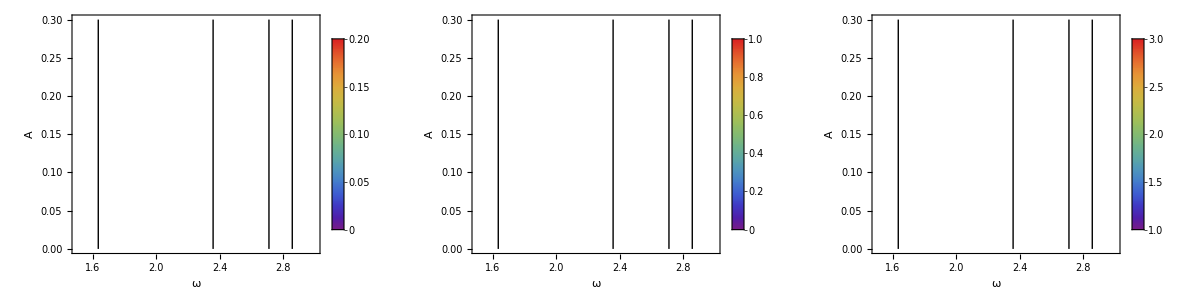

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```